```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/675nm.dat"]
```

{{1.50189,0.20872},{1.45414,0.208071},{1.33983,0.218493},{1.30748,0.226019},{1.27821,0.227693},{1.24682,0.198769},{1.22351,0.143234},{1.20659,0.0922145},{1.18213,0.00149888},{1.16419,-0.0602809},{1.15263,-0.0943436},{1.13304,-0.14937},{1.09662,0.177141},{1.09807,0.152721},{1.10207,0.15315},{1.10747,0.159565},{1.11401,0.162969},{1.12685,0.168054},{1.13867,0.182322},{1.15401,0.185732},{1.16573,0.178983},{1.20258,0.18382},{1.26466,0.185649},{1.30748,0.181321},{1.33983,0.16873},{1.37936,0.176639}}

-0.274813+0.339207 x

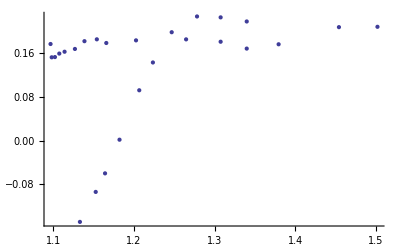

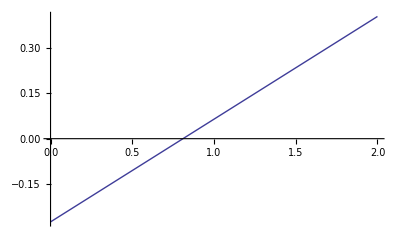

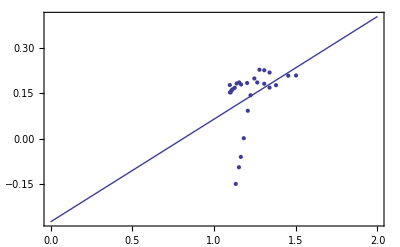

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```